```mathematica
ClearAll["Global`*"];
```

```mathematica
dataSelfing=Import[NotebookDirectory[]<>"../Data/"<>"Table_MGWP_Selfing_n4.txt","CSV"];
```

## Escape year distribution under cross- and self-pollination

```mathematica
partitionedData=Partition[dataSelfing⟦2;;⟧,Max[dataSelfing[[2;;,2]]]];
```

```mathematica
RW=Table[DeleteCases[partitionedData⟦i,All,11⟧,"NaN"],{i,1,Length[partitionedData]}];
```

```mathematica
RR=Table[DeleteCases[partitionedData⟦i,All,12⟧,"NaN"],{i,1,Length[partitionedData]}];
```

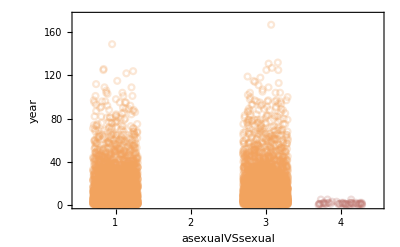

```mathematica
ListPlot[MapIndexed[{#2[[1]]+RandomReal[{-0.3,0.3}],#1}&,{RW[[1]],Prepend[RR[[1]],-10],RW[[3]],RR[[3]]},{2}],PlotMarkers->Graphics[{Circle[]},ImageSize->6],PlotStyle->{Directive[PointSize[0.015],Opacity[0.25],RGBColor["#F2A35E"]],Directive[PointSize[0.015],Opacity[0.25],RGBColor["#BF766F"]],Directive[PointSize[0.015],Opacity[0.25],RGBColor["#F2A35E"]],Directive[PointSize[0.015],Opacity[0.25],RGBColor["#BF766F"]]},PlotRange->{{0.5,4.5},{0,175}},Frame->True,FrameTicks->{Range[1,4,1],Automatic},FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"asexualVSsexual","year"}]
```